```mathematica
V = (4.8^2)/2
p [e_]:=Sqrt[2e]
k[e_]:=Sqrt[2e+V]
RiccatiBessel[l_,z_]:=z*SphericalBesselJ[l,z]
RiccatiNeumann[l_,z_]:=z*SphericalBesselY[l,z]
DRiccatiBessel[l_,z_]:=D[zz*SphericalBesselJ[ll,zz],{zz,1}]/.{ll->l,zz->z}
DRiccatiNeumann[l_,z_]:=D[zz*SphericalBesselY[ll,zz],{zz,1}]/.{ll->l,zz->z}
l = 0

gamma[e_]:=(k[e]*DRiccatiBessel[l,k[e]])/RiccatiBessel[l,k[e]]
delta[e_]:=ArcTan[(-gamma[e]*RiccatiBessel[l,p[e]]+p[e]*DRiccatiBessel[l,p[e]])/(gamma[e]*RiccatiNeumann[l,p[e]]-p[e]*DRiccatiNeumann[l,p[e]])]
sigma[e_]:=4*Pi/(2*e)*(2*l+1)*Sin[delta[e]]^2
```

11.52

0

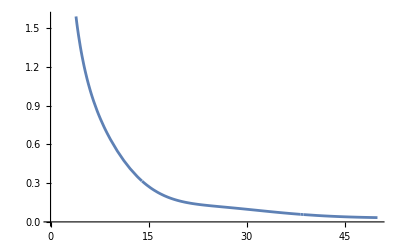

```mathematica
Plot[sigma[e],{e,0,50}]
```

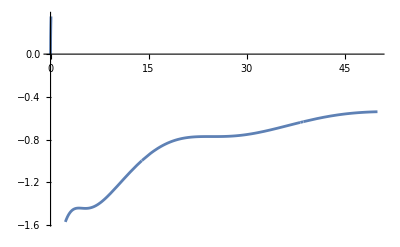

```mathematica
Plot[delta[e]+Pi,{e,0,50}]
```